# L5 - Symbolic maths: Mathematica

### Q3: Solve the equation x ln(x) - 3 x + 10 = 6, both symbolically and numerically.

Symbolical solutions using Solve are:

```mathematica
sol=Solve[x Log[x]-3 x+10==6,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-4/ProductLog[-4/ⅇ^3]},{x→-4/ProductLog[-1,-4/ⅇ^3]}}

So the two solutions are:

```mathematica
N[sol]
```

{{x→15.5229},{x→1.56883}}

I plot the function between 0.1 and 20 to have another guess of the x values to put in FindRoot:

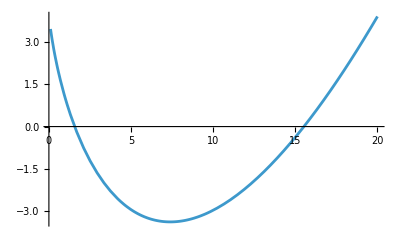

```mathematica
Plot[x Log[x]-3x+10-6,{x,0.1,20}]
```

I find numerical solutions with FindRoot:

```mathematica
FindRoot[x Log[x]-3 x+10==6,{x,1.5}]
```

{x→1.56883}

```mathematica
FindRoot[x Log[x]-3 x+10==6,{x,15.5}]
```

{x→15.5229}

Solve and FindRoot give the same two roots.

### Q4: Solve the following initial-value problem using both DSolve and NDSolve. Compare your answers by plotting them. y’’(x) - x y(x) = 0 y(0) = 1 y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3) (bonus: solve it with scipy and check result and speed).

Using DSolve:

```mathematica
ds = DSolve[{y''[x]-x y[x]==0,y[0]==1,y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},y,x]
plot1=(y/. Flatten@ds)[x]
```

{{y→Function[{x},3^(2/3) AiryAi[x] Gamma[2/3]]}}

3^(2/3) AiryAi[x] Gamma[2/3]

Using NDSolve:

```mathematica
nds = NDSolve[{y''[x]-x y[x]==0,y[0]==1,y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},y,{x,-20,5}]
plot2=(y/. Flatten@nds)[x]
```

{{y→InterpolatingFunction[…]}}

InterpolatingFunction[…][x]

I plot both functions to compare them (I choose an arbitrary x range):

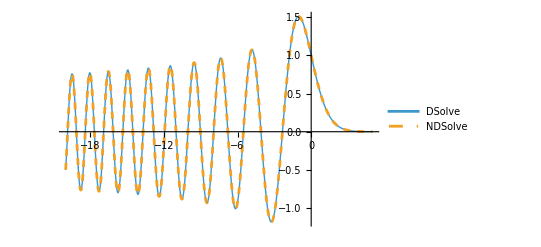

```mathematica
Plot[{plot1,plot2},{x,-20,5},PlotStyle->{Thick,Dashed},PlotLegends->{"DSolve","NDSolve"}]
```

NDSolve and DSolve curves are exactly the same, thus the two solutions agree